## Dicke Hamiltonian, Reduced Basis

### Jz, J+, J- Construction

```mathematica
Jz[K_Integer]:=Module[{J,dim,Jz},
J=K/2;
dim=2 J+1;
Jz=SparseArray[DiagonalMatrix[Reverse[Range[-J,J]]]];
Return[Jz];
]

Jp[K_Integer]:=Module[{J,dim,Jplus,mValues,i,j},
J=K/2;
dim=2 J+1;
Jplus=SparseArray[{},{dim,dim}];
mValues=Reverse[Range[-J,J]];
For[i=1,i<dim,i++,
Jplus[[i,i+1]]=Sqrt[J * (J+1) - mValues[[i+1]] * (mValues[[i+1]]+1)];
];
Return[SparseArray[Jplus]];
]

Jm[K_Integer]:=Module[{J,dim,Jplus,mValues,i,j},
J=K/2;
dim=2 J+1;
Jplus=SparseArray[{},{dim,dim}];
mValues=Reverse[Range[-J,J]];
For[i=2,i<=dim,i++,
Jplus[[i,i-1]]=Sqrt[J * (J+1) - mValues[[i]] * (mValues[[i]]+1)];
];
Return[Jplus];
]
```

### Complete Construction

```mathematica
(*Constants*)
bsize=30;ω0=1.0; ωc = 1.0;j = 0.07;K = 5;
(*Identity matrix for QHO*)
idHO=SparseArray[IdentityMatrix[bsize]];
idTLS = SparseArray[IdentityMatrix[K + 1]];


(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*Combined TLS Hamiltonian*)
HTLS = ω0 * Jz[K];
(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

Hindep = KroneckerProduct[HTLS, idHO] + KroneckerProduct[idTLS, H0HO];
Hcoup = j*(KroneckerProduct[Jp[K], a] + KroneckerProduct[Jm[K], a†]+KroneckerProduct[Jp[K], a†] + KroneckerProduct[Jm[K], a]);
Htot = Hindep + Hcoup;
```

## Initial States, Observables Construction

### Initial States

```mathematica
(*QHO*)
ψ0HO=SparseArray[{1->1.0},bsize];
(*TLS*)
ψ0TLS = SparseArray[{1->1.0},K + 1]; (*Second Excitation Manifold*)
Print[ψ0TLS //MatrixForm];
ψ0vec = KroneckerProduct[ψ0TLS, ψ0HO] //Flatten;
Print[Norm[ψ0vec]];
```

(1.
0
0
0
0
0)

1.

### Observable Matrices

#### Oscillator Position

```mathematica
xM = KroneckerProduct[IdentityMatrix[K + 1],1/Sqrt[2](a†+a)];
ConjugateTranspose[ψ0vec].xM.ψ0vec
```

0.

## Propagation

### Calculating States

```mathematica
stateVector[t_] := MatrixExp[-I * Htot * t, ψ0vec];
tMax =2000; 
tRange=Range[0,tMax,1];
ψs=ParallelTable[stateVector[t],{t,tRange}];
```

### Photon Number Expectation in Cavity

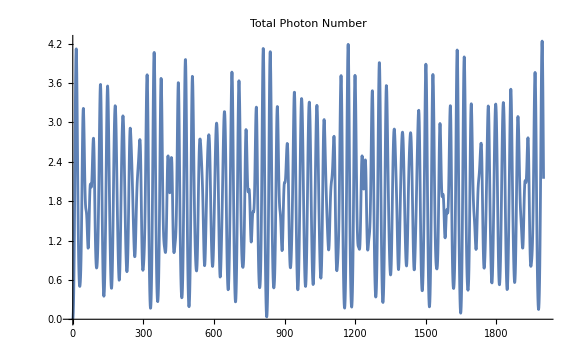

```mathematica
aDaggerA=KroneckerProduct[IdentityMatrix[K+1],a†.a];
aDaggerAsr = aDaggerA.aDaggerA;
photons=Table[Conjugate[ψs[[n]]].aDaggerA.ψs[[n]],{n,Length@tRange}];
ListLinePlot[{tRange,photons//Re}//Transpose,PlotRange->All,PlotLabel->"Total Photon Number", ImageSize->Large]
```

### Photon Statistics, Variance

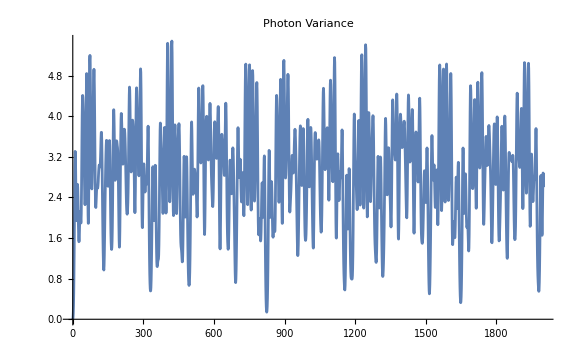

```mathematica
newPhotons=Table[Conjugate[ψs[[n]]].aDaggerAsr.ψs[[n]],{n,Length@tRange}] - photons^2;
ListLinePlot[{tRange,newPhotons//Re}//Transpose,PlotRange->All,PlotLabel->"Photon Variance", ImageSize->Large]
```

### Excitation Spectrum

Eigenvalues::arh: Because finding 180 out of the 180 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

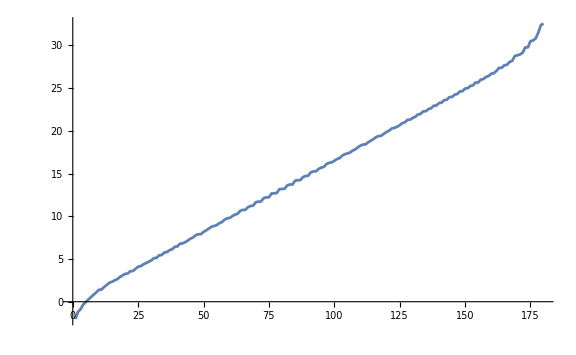

```mathematica
eigv = Eigenvalues[N[Htot]];
ListLinePlot[{Sort[eigv]}, PlotRange->All, ImageSize->Large]
```